7 Ecuaciones y sistemas
7.1 Los comandos fundamentales

```mathematica
Solve[3x+8==0]
Reduce[3x+8==0] (* Equivalente a Solve *)
```

{{x→-8/3}}

x==-8/3

```mathematica
Solve[(3-x)/3+(4x-1)/7==4]
NSolve[(3-x)/3+(4x-1)/7==4] (* Decimal *)
```

{{x→66/5}}

{{x→13.2}}

```mathematica
Solve[a*x+b==0,x] (* Indicar la variable sobre la que se resolverá en caso de haber parámetros u otras variables *)
Solve[a*x+b==0,a]
Solve[a*x+b==0,b]
```

{{x→-b/a}}

{{a→-b/x}}

{{b→-a x}}

7.2 Ecuaciones algebraicas

```mathematica
Solve[x^2-5x+6==0] (* Dos soluciones reales *)
Solve[x^2+2x+1==0] (* Una solución real *)
Solve[x^2-4x+5==0] (* Soluciones complejas conjugadas *)
```

{{x→2},{x→3}}

{{x→-1},{x→-1}}

{{x→2-ⅈ},{x→2+ⅈ}}

```mathematica
Solve[a*x^2+b*x+c==0,x]
Solve[x^5-6x^4+10x^3-10x^2+9x-4==0]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

{{x→-ⅈ},{x→ⅈ},{x→1},{x→1},{x→4}}

```mathematica
Solve[x^5+x^4+x^3+x^2+x+4==0] (* No encuentra una solución exacta *)
```

{{x→Root[4+#1+#1^2+#1^3+#1^4+#1^5&,1]},{x→Root[4+#1+#1^2+#1^3+#1^4+#1^5&,2]},{x→Root[4+#1+#1^2+#1^3+#1^4+#1^5&,3]},{x→Root[4+#1+#1^2+#1^3+#1^4+#1^5&,4]},{x→Root[4+#1+#1^2+#1^3+#1^4+#1^5&,5]}}

```mathematica
NSolve[x^5+x^4+x^3+x^2+x+4==0] 
NSolve[x^5+x^4+x^3+x^2+x+4==0, WorkingPrecision->20]
```

{{x→-1.42194},{x→-0.569917-1.2543 ⅈ},{x→-0.569917+1.2543 ⅈ},{x→0.780887-0.933957 ⅈ},{x→0.780887+0.933957 ⅈ}}

{{x→-1.4219389943378197933},{x→-0.5699172240852904616-1.2543005566923667028 ⅈ},{x→-0.5699172240852904616+1.2543005566923667028 ⅈ},{x→0.7808867212542003582-0.93395667941862406799 ⅈ},{x→0.7808867212542003582+0.93395667941862406799 ⅈ}}

7.3 Sistemas con n variables y n ecuaciones

```mathematica
Solve[{3x+7y==9,-5x+9y==5},{x,y}]  (* Una única solución *)
Solve[{3x+7y==9,-5x+9y==5}]
```

{{x→23/31,y→30/31}}

{{x→23/31,y→30/31}}

```mathematica
Solve[{x+y==0,x+y==1}] (* Sin solución *)
```

{}

```mathematica
Solve[{x+y==1,2x+2y==2},{x,y}]  (* Infinitas soluciones *)
Solve[{x+y==1,2x+2y==2},{x}] 
Solve[{x+y==1,2x+2y==2},{y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→1-x}}

{{x→1-y}}

{{y→1-x}}

```mathematica
Solve[{x^2-46x==8,-6x+7y==-3}] (* Sistema no lineal *)
NSolve[{x^2-46x==8,-6x+7y==-3}]
```

{{x→23-√537,y→3/7 (45-2 √537)},{x→23+√537,y→3/7 (45+2 √537)}}

{{x→-0.17326,y→-0.57708},{x→46.1733,y→39.1485}}

7.4 Sistemas con más variables que ecuaciones

```mathematica
Solve[{6x+9y-3z==8,3x-8y+9z==7},{x,y,z}]
Solve[{6x+9y-3z==8,3x-8y+9z==7},{x,y}]
Solve[{6x+9y-3z==8,3x-8y+9z==7},{x,z}]
Solve[{6x+9y-3z==8,3x-8y+9z==7},{y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→31/19-(21 x)/19,z→127/57-(25 x)/19}}

{{x→1/75 (127-57 z),y→3/25 (-2+7 z)}}

{{x→1/21 (31-19 y),z→1/21 (6+25 y)}}

{{y→1/19 (31-21 x),z→1/57 (127-75 x)}}

7.5 Otros tipos de  ecuaciones algebraicas

```mathematica
Solve[1+Sqrt[3x+4]==x+1,x]
```

{{x→4}}

```mathematica
Solve[6/(x^2-1)-2/(x-1)==2-(x+4)/(x-1)]
```

{{x→-2},{x→5}}

7.6 Ecuaciones no algebraicas

```mathematica
Solve[x^2-1==0]
Solve[Cos[x^2]-6x==Tan[x]]
```

{{x→-1},{x→1}}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[-6 x+Cos[x^2]==Tan[x]]
```

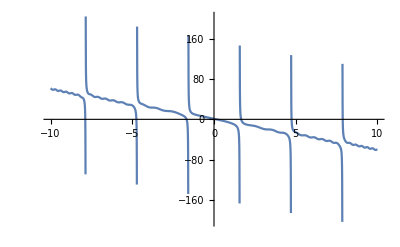

```mathematica
Plot[-6 x+Cos[x^2]==Tan[x],{x,-10,10}]
```

```mathematica
FindRoot[-6 x+Cos[x^2]==Tan[x],{x,3}] (* Semilla x=3 *)
FindRoot[-6 x+Cos[x^2]==Tan[x],{x,-2}] (* Semilla x=9 *)
FindRoot[-6 x+Cos[x^2]==Tan[x],{x,10}, WorkingPrecision->20] (* Semilla x=10 *)
```

{x→0.142688}

{x→-1.67989}

{x→11.010646297053051482}

```mathematica
Plot3D[{y==Exp[x],x+y==2},{x,-10,10},{y,-10,10}, AxesLabel->Automatic]
FindRoot[{y==Exp[x],x+y==2},{{x,1},{y,2}}] (* Semillas: x=1, y=2 *)
```

-Graphics3D-

{x→0.442854,y→1.55715}

7.7 Inecuaciones
Solo funciona Reduce[ ]

```mathematica
Reduce[4x-5>9,x]
Reduce[x^2-5x≥ -6]
Reduce[x^2-5x≥ -6]//TraditionalForm
Reduce[(x^2-5x+6)/(x^2-6x+8)≥0]
```

x>7/2

x≤2||x≥3

x≤2∨x≥3

x≤3||x>4